```mathematica
Clear["Global`*"]
```

# From spheroidal to spherical mode amplitudes

Goal: turn the Teukolsky amplitudes C^up_ℓ'm, which the Teukolsky package returns in the basis of spin-weighted spheroidal harmonics ₋₂S_ℓ'm(θ;γ), into amplitudes C_ℓm in the basis of spin-weighted spherical harmonics ₋₂Y_ℓm(θ), the basis of the PN waveform. This is Honet+ 2025 App. A3, eqs. (A24)-(A31).

Roadmap: (0) conventions, (1) spherical vs spheroidal harmonics, (2) why the change of basis is a matrix μ, (3) μ by brute-force overlap integrals, (4) μ by the spectral method (what the package does inside), (5) making sure μ refers to the same S the Teukolsky amplitude was computed with, (6) the change of basis at one orbit, with checks, (7) truncation in ℓ', (8) what the production code for the Honet grid needs.

Each exercise has an empty input cell for your attempt and a closed "Solution" group below it (double-click the group bracket to open it). Later sections use functions defined in earlier solutions, so evaluate the solutions in order if you skip an exercise.

```mathematica
Needs["KerrGeodesics`"];Needs["Teukolsky`"];Needs["SpinWeightedSpheroidalHarmonics`"];
s=-2;
Y[l_,m_,θ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,0];
```

## 0. Conventions

Honet+ eq. (A1): for a point mass on a circular equatorial orbit with angular freq9ouency Ω, Ψ4 is decomposed in spheroidal harmonics. Each m oscillates at the single frequency ω = mΩ, and the spheroidicity of the angular functions is

γ_m==a ω==a m Ω

ζ^4 Ψ_4==∑_(ℓ'=2)^∞ ∑_(m=-ℓ')^ℓ' R_(ℓ' m)(r) S_(ℓ' m)(θ,φ,γ_m) exp(-ⅈ m Ω t)

with ζ = r - i a cosθ. Far from the source, , and Honet (A24) defines the spheroidal waveform modes as

(h̃)_(ℓ' m)==(2 C_(ℓ' m)^up)/(m Ω)^2

Three facts make the change of basis simple:

At r → ∞, ζ⁴ → r⁴(1 + O(1/r)), so all angular dependence of the 1/r part sits in S_ℓ'm. The change of basis is purely angular.

It is linear, so the same matrix μ acts on Ψ4, on C^up and on h̃. We work with C^up = md["Amplitudes"]["ℐ"].

m is the same in both bases (both carry e^{imφ}). For a circular orbit there is one γ_m per m, shared by all ℓ'. So for each m you need one matrix μ_{ℓℓ'}(γ_m), not one per mode.

In the package, a ≥ 0 always, and retrograde orbits have x = -1 (as in FluxesGrid.nb). Honet instead uses a signed χ with Ω̂ > 0. Section 5 checks that both give the same γ_m.

## 1. Spherical vs spheroidal harmonics

₋₂S_ℓm(θ;γ) solves the angular Teukolsky equation (s = -2, eigenvalue A):

(∂/(∂θ)(sin(θ) (∂S)/(∂θ)))/(sin(θ))+(γ^2 cos^2(θ)-2 γ s cos(θ)-(m+s cos(θ))^2/(sin^2(θ))+s+A) S==0

At γ = 0 the γ terms drop out and S = ₛY_ℓm with A = ℓ(ℓ+1) - s(s+1). The package's SpinWeightedSpheroidalEigenvalue returns λ = A + γ.b2 - 2mγ, not A. Both S and Y include e^{imφ} and are normalised to 1 over the sphere. In this notebook we set φ = 0 and write ∫dΩ = 2π∫ sinθ dθ, because the e^{imφ} factors cancel in every overlap at fixed m.

```mathematica
Sg=SpinWeightedSpheroidalHarmonicS[s,2,2,0.5`30]
```

SpinWeightedSpheroidalHarmonicSFunction[…]

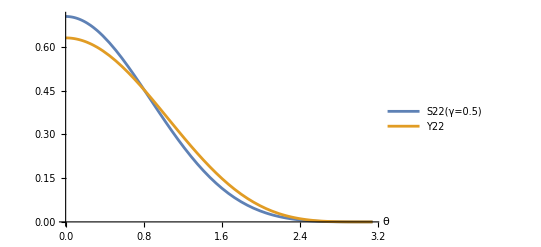

```mathematica
Plot[{Sg[θ,0],Y[2,2,θ]},{θ,0,π},PlotLegends->{"S22(γ=0.5)","Y22"},AxesLabel->{"θ",""}]
```

At fixed γ the S_ℓm (ℓ = 2, 3, ...) form an orthonormal basis: they are eigenfunctions of a self-adjoint operator. S's at different γ are not orthogonal to each other. That is exactly why expanding one in terms of the other (Y = S at γ = 0) gives a non-trivial matrix.

### Exercise 1

(a) Check that SpinWeightedSpheroidalHarmonicS[s, l, 2, 0] equals Y[l, 2, θ] for l = 2..5 at θ = 0.7. (b) Write an inner product ip[f, g] = 2π ∫ f(θ)* g(θ) sinθ dθ (NIntegrate, f and g pure functions of θ). With it, check ⟨S₂₂|S₂₂⟩ = 1 and ⟨S₂₂|S₃₂⟩ = 0 at γ = 0.5. (c) Compute ⟨Y₂₂|S₂₂(γ=0.5)⟩ and ⟨Y₃₂|S₂₂(γ=0.5)⟩. These numbers are your first two mixing coefficients.

```mathematica
SgEx1=SpinWeightedSpheroidalHarmonicS[s,l,2,0];
Table[FullSimplify[SpinWeightedSpheroidalHarmonicS[s,l,2,0][θ,ϕ]-SpinWeightedSphericalHarmonicY[-2,l,2,θ,ϕ]],{l,2,10}]

InnProd[f_,g_]:=NIntegrate[Conjugate[f[θ,ϕ]]*g[θ,ϕ]*Sin[θ],{θ,0,π},{ϕ,0,2 π},Method->"LocalAdaptive"]
S21[θ_,ϕ_]=SpinWeightedSpheroidalHarmonicS[s,2,1,0.5][θ,ϕ];
S22[θ_,ϕ_]=SpinWeightedSpheroidalHarmonicS[s,2,2,0.5][θ,ϕ];
S32[θ_,ϕ_]=SpinWeightedSpheroidalHarmonicS[s,3,2,0.5][θ,ϕ];
Y21[θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,2,1,θ,ϕ];
Y22[θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,2,2,θ,ϕ];
Y32[θ_,ϕ_]:=SpinWeightedSphericalHarmonicY[s,3,2,θ,ϕ];
InnProd[S22,S22]
InnProd[S22,S32]
InnProd[S21,S22]

InnProd[Y22,S22]
InnProd[Y32,S22]
InnProd[Y21,S22]
(*InnProd[Y22,Y22]
InnProd[Y22,Y32]*)
```

{0,0,0,0,0,0,0,0,0}

1.

-4.24242×10^-10

7.28448×10^-17-1.14492×10^-16 ⅈ

0.995552

0.0939677

2.94632×10^-17-9.02056×10^-17 ⅈ

```mathematica
(* setting phi=0*)
InnProd2[f_,g_]:=2π NIntegrate[Conjugate[f[θ]]*g[θ]*Sin[θ],{θ,0,π},WorkingPrecision->25,PrecisionGoal->12,AccuracyGoal->15]
(*PrecisionGoal -> Teukolsky amplitudes are accurate to ~12 digits 
AccuracyGoal -> So that integrator doesn't take too much time computing small quantities to PrecGoal
WorkingPrecision -> Default is MachinePrecision=16, a bit too close to PrecGoal=12. This is a conservative choice but still not the 30 digits used in γ, so the integrator is not the problem*) 
S21[θ_]=SpinWeightedSpheroidalHarmonicS[s,2,1,0.5][θ,0];
S22[θ_]=SpinWeightedSpheroidalHarmonicS[s,2,2,0.5][θ,0];
S32[θ_]=SpinWeightedSpheroidalHarmonicS[s,3,2,0.5][θ,0];
Y21[θ_]:=SpinWeightedSphericalHarmonicY[s,2,1,θ,0]
Y22[θ_]:=SpinWeightedSphericalHarmonicY[s,2,2,θ,0];
Y32[θ_]:=SpinWeightedSphericalHarmonicY[s,3,2,θ,0];
InnProd2[S22,S22]
InnProd2[S22,S32]
InnProd2[S21,S22]
InnProd2[Y22,S22]
InnProd2[Y32,S22]
InnProd2[Y21,S22]
```

1.000000000000000522538164

8.233791215418583468158825×10^-16

0.8587871521844132542260755

0.9955517758526891588238224

0.09396768359818684139308356

0.8074306560763945318175471

#### Solution

```mathematica
Table[SpinWeightedSpheroidalHarmonicS[s,l,2,0][0.7,0]-Y[l,2,0.7],{l,2,5}]
```

{0.,0.,0.,0.}

```mathematica
ip[f_,g_]:=2πNIntegrate[Conjugate[f[θ]]g[θ]Sin[θ],{θ,0,π},WorkingPrecision->25,PrecisionGoal->12,AccuracyGoal->15]
```

```mathematica
S22=SpinWeightedSpheroidalHarmonicS[s,2,2,0.5`30];S32=SpinWeightedSpheroidalHarmonicS[s,3,2,0.5`30];
{ip[S22[#,0]&,S22[#,0]&],ip[S22[#,0]&,S32[#,0]&]}
```

{0.9999999999999999999993738,1.932475662061598671278869×10^-30}

```mathematica
{ip[Y[2,2,#]&,S22[#,0]&],ip[Y[3,2,#]&,S22[#,0]&]}
```

{0.9955517758526887842397876,0.09396768359818681198798503}

The first is close to 1 and the second is small but non-zero: S₂₂ "leaks" into ℓ = 3. Both are real because γ is real and φ = 0.

## 2. Why a change of basis is a matrix

Expand each spheroidal harmonic in spherical ones at the same m and the same γ = γ_m:

S_(ℓ' m)(θ,γ_m)==∑_(ℓ=max(2,Abs[m]))^∞ μ_(ℓ,ℓ') Y_(ℓ m)(θ)

μ_(ℓ,ℓ')==∫Conjugate[(Y_(ℓ m))] S_(ℓ' m)ⅆΩ

Insert this into Σ_ℓ' C_ℓ'm S_ℓ'm and collect the coefficient of Y_ℓm. That gives Honet (A25):

C_(ℓ m)==∑_(ℓ'=max(2,Abs[m]))^∞ μ_(ℓ,ℓ')(γ_m) C_(ℓ' m)

Column ℓ' of μ holds the spherical components of S_ℓ'. Both bases are orthonormal, so μ is orthogonal (real for real γ): μᵀμ = 1 for the infinite matrix. In practice both sums are truncated (Section 7). Its entries fall off like γ^|ℓ-ℓ'|, so μ is close to the identity for small γ.

Symmetry under m → -m. Equatorial circular orbits have γ_{-m} = -γ_m, and the mixing matrices are related by

μ_(ℓ,ℓ')(-m,-γ)==(-1)^(ℓ+ℓ') μ_(ℓ,ℓ')(m,γ)

so you only ever need m > 0 (m = 0 modes are excluded in Honet, since (A24) is singular there).

## 3. μ by brute force

The definition in Section 2 is an integral, so the most direct (slow) route is NIntegrate. Keep this as ground truth for the faster method.

### Exercise 2

Write muBF[l, lp, m, γ] = ⟨Y_lm|S_lp,m(γ)⟩ using ip from Exercise 1. Tabulate muBFtab = μ_{ℓℓ'} for m = 2, γ = 0.5`30 and ℓ, ℓ' = 2..6 (rows ℓ, columns ℓ'). Look at how fast entries decay away from the diagonal, and check whether Transpose[muBFtab].muBFtab is close to the identity. Which entries deviate most, and why?

```mathematica
muBF[l_,lp_,m_,γ_]:=Module[
{S,Y},
S[θ_]=SpinWeightedSpheroidalHarmonicS[-2,lp,m,γ][θ,0];
Y[θ_]=SpinWeightedSphericalHarmonicY[-2,l,m,θ,0];
InnProd2[Y,S]
]
```

```mathematica
m=2;
ellmin=Max[2,Abs[m]];
ellmax=6;
muBFTab=Table[muBF[l,lp,m,0.5`30],{l,ellmin,ellmax},{lp,ellmin,ellmax}];
muBFTab//MatrixForm
Transpose[muBFTab].muBFTab//MatrixForm
Chop[Transpose[muBFTab].muBFTab-IdentityMatrix[ellmax-ellmin+1],10^-8]//MatrixForm
Clear[m,ellmin,ellmax]
```

(0.9955517758526887842397876 | -0.09418650174534145757752481 | 0.002358377036663749080591484 | 0.00005039393300617924559899646 | -1.933030625459656251998708×10^-6
0.09396768359818681198798503 | 0.9908019103857739119312679 | -0.09735982809015553368437505 | 0.001645280534853195321926766 | 0.00007575116204348946441889835
0.006825320105076600871161121 | 0.09692346292351140363964668 | 0.9914841529634574154156301 | -0.08670422904399955621604045 | 0.0008957843143178606155203611
0.0003882124821987940067369669 | 0.006796578764012350973117351 | 0.08626895820719174990532889 | 0.9933508071238598767368311 | -0.07592983508501304575720508
0.00001821420606061891901170643 | 0.000354797511492643731331903 | 0.005680693134864296957988781 | 0.07557700306429114809060769 | 0.9948778783770516697417088)

(0.999999999999476638106864 | -1.1104703135976×10^-11 | -1.953648253968776×10^-10 | -3.389828346779565611×10^-9 | -4.82552239174522164203×10^-8
-1.1104703135976×10^-11 | 0.999999999764379241879055 | -4.1453014944920944×10^-9 | -7.192673786168594816×10^-8 | -1.02392997124001694964×10^-6
-1.953648253968776×10^-10 | -4.1453014944920944×10^-9 | 0.999999927070303014488861 | -1.265446869103244206×10^-6 | -0.0000180155627129042378092
-3.389828346779565611×10^-9 | -7.192673786168594816×10^-8 | -1.265446869103244206×10^-6 | 0.999978042227504926472405 | -0.0003126182576446234894783
-4.82552239174522164203×10^-8 | -1.02392997124001694964×10^-6 | -0.0000180155627129042378092 | -0.0003126182576446234894783 | 0.995548140911573828659422)

(0 | 0 | 0 | 0 | -4.82552239174522164203×10^-8
0 | 0 | 0 | -7.192673786168594816×10^-8 | -1.02392997124001694964×10^-6
0 | 0 | -7.2929696985511139×10^-8 | -1.265446869103244206×10^-6 | -0.0000180155627129042378092
0 | -7.192673786168594816×10^-8 | -1.265446869103244206×10^-6 | -0.000021957772495073527595 | -0.0003126182576446234894783
-4.82552239174522164203×10^-8 | -1.02392997124001694964×10^-6 | -0.0000180155627129042378092 | -0.0003126182576446234894783 | -0.004451859088426171340578)

#### Solution

```mathematica
muBF[l_,lp_,m_,γ_]:=With[{Sf=SpinWeightedSpheroidalHarmonicS[s,lp,m,γ]},ip[Y[l,m,#]&,Sf[#,0]&]]
```

```mathematica
g=0.5`30;
muBFtab=Table[muBF[l,lp,2,g],{l,2,6},{lp,2,6}];
N[muBFtab,6]//MatrixForm
```

(0.995552 | -0.0941865 | 0.00235838 | 0.0000503939 | -1.93303×10^-6
0.0939677 | 0.990802 | -0.0973598 | 0.00164528 | 0.0000757512
0.00682532 | 0.0969235 | 0.991484 | -0.0867042 | 0.000895784
0.000388212 | 0.00679658 | 0.086269 | 0.993351 | -0.0759298
0.0000182142 | 0.000354798 | 0.00568069 | 0.075577 | 0.994878)

```mathematica
Chop[Transpose[muBFtab].muBFtab-IdentityMatrix[5],10^-8]//N//MatrixForm
```

(0. | 0. | 0. | 0. | -4.82552×10^-8
0. | 0. | 0. | -7.19267×10^-8 | -1.02393×10^-6
0. | 0. | -7.29297×10^-8 | -1.26545×10^-6 | -0.0000180156
0. | -7.19267×10^-8 | -1.26545×10^-6 | -0.0000219578 | -0.000312618
-4.82552×10^-8 | -1.02393×10^-6 | -0.0000180156 | -0.000312618 | -0.00445186)

The deviation sits in the last column(s): S₆₂ has components on Y₇₂, Y₈₂, ... that the 5×5 table leaves out. Truncating rows loses norm. Keep this in mind for Section 7.

## 4. μ by the spectral method

Section 3 computed μ from overlap integrals of S. The spectral method never evaluates S at all. It rewrites the angular Teukolsky equation as an eigenvalue problem for a matrix in the Y basis, and the eigenvectors of that matrix are the columns of μ.

Split the angular operator of Section 1 as L₀ + γ.b2 cos.b2θ - 2γs cosθ, where L₀ is the γ = 0 part. L₀ is diagonal on the Y's: L₀ Y_ℓ = -(ℓ(ℓ+1) - s(s+1)) Y_ℓ. The two γ terms are multiplications by cosθ and cos.b2θ. These are not diagonal: cosθ Y_ℓ is a combination of Y_{ℓ-1}, Y_ℓ and Y_{ℓ+1}. Their matrix elements in the Y basis are called c1 and c2:

c1_(ℓ,ℓ'')==∫Conjugate[(Y_(ℓ m))] cos(θ) Y_(ℓ'' m)ⅆΩ

c2_(ℓ,ℓ'')==∫Conjugate[(Y_(ℓ m))] cos^2(θ) Y_(ℓ'' m)ⅆΩ

So c1 is the matrix of cosθ and c2 the matrix of cos.b2θ, at fixed m and s. Both are real and symmetric and do not depend on γ: all the γ dependence sits in the explicit factors γ and γ.b2.

Now insert S_ℓ' = Σ_ℓ'' μ_ℓ''ℓ' Y_ℓ'' into the angular equation (eigenvalue A_ℓ'), multiply by Y_ℓ* and integrate over the sphere. L₀ gives the diagonal term, the γ terms give c1 and c2:

∑_(ℓ''=max(2,Abs[m]))^∞ ((ℓ (ℓ+1)-s (s+1)) ℓ,ℓ''-γ^2 c2_(ℓ,ℓ'')+2 γ s c1_(ℓ,ℓ'')) μ_(ℓ'',ℓ')==A_ℓ' μ_(ℓ,ℓ')

In words: build the matrix M = diag(ℓ(ℓ+1) - s(s+1)) - γ.b2 c2 + 2γs c1. Its eigenvalues are the spheroidal eigenvalues A_ℓ' and its eigenvectors are the columns of μ. At γ = 0, M is diagonal and μ = 1, as it should be. What is left is to compute c1 and c2.

c1 has a closed form. Write cosθ = √(4π/3) ₀Y₁₀. The integral of three spin-weighted harmonics is a product of two Clebsch–Gordan coefficients, one carrying m and one carrying the spin weight -s:

c1_(ℓ,ℓ'')==√((2 ℓ''+1)/(2 ℓ+1)) ⟨ℓ'' 1 m 0 | ℓ'' 1 ℓ m⟩ ⟨ℓ'' 1 -s 0 | ℓ'' 1 ℓ -s⟩

The first Clebsch–Gordan coefficient vanishes unless |ℓ - ℓ''| ≤ 1, so c1 is tridiagonal. Its diagonal is c1_ℓℓ = -ms/(ℓ(ℓ+1)), nonzero because s ≠ 0. For c2, use cos.b2θ = cosθ · cosθ and insert a complete set of Y_k in between: c2 is the matrix product of c1 with itself.

c2_(ℓ,ℓ'')==∑_(k=max(2,Abs[m]))^∞ c1_(ℓ,k) c1_(k,ℓ'')

c2 couples ℓ to ℓ'' up to ℓ ± 2, so M is pentadiagonal. Careful when truncating: in practice M is built on a finite range ℓ = ℓmin … ℓmax. Squaring the truncated c1 matrix does not give c2 there: in the last rows the intermediate state k = ℓmax + 1 is missing and the entries come out wrong. Compute each c2 entry with the sum over k running up to max(ℓ, ℓ'') + 1, wherever the matrix is cut (the solution's c2 does this).

Two bookkeeping choices fix μ completely. Labels: which eigenvector is which ℓ'? For real γ the angular equation is a 1D Sturm–Liouville problem, whose eigenvalues are non-degenerate, so they cannot cross as γ grows from 0. At γ = 0 they are ordered by ℓ. So sort the eigenvalues in increasing order and assign ℓ' = ℓmin, ℓmin+1, … Signs: each eigenvector is defined only up to an overall sign. The package picks the sign that makes the diagonal entry μ_ℓ'ℓ' positive, so that S_ℓ' → +Y_ℓ' as γ → 0. Section 5 checks that this matches the S used for the Teukolsky amplitudes.

This is what the package does in SWSHSSpectral (SpinWeightedSpheroidalHarmonics.m, around line 519). Its matrix is -(M + s(s+1)·1), which has the same eigenvectors: kHat is the diagonal, kTilde2 the ±1 and k2 the ±2 off-diagonal entries. For S_ℓ' it truncates to a window ℓ = ℓ' - nDown … ℓ' + nUp around ℓ', not to a fixed range starting at ℓmin.

### Exercise 3

(a) Implement c1[m, l, lp] and c2[m, l, lp] from the formulas above (ClebschGordan complains when the triangle rule fails, so return 0 for |l - lp| > 1 by hand. Only in c1 (for c2 it would be >0)). Check one element of each against ip. (b) Build specMatrix[m, γ, lmaxB] on ℓ = ℓmin..lmaxB, diagonalise it, and sort the eigenvalues. Compare A + γ.b2 - 2mγ with SpinWeightedSpheroidalEigenvalue for ℓ = 2..5. (c) Fix the eigenvector signs so the diagonal entries are positive, and compare the 5×5 block of μ with muBFtab.

```mathematica
c1[m_,l_,lp_]:=If[Abs[l-lp]>1,0,√((2lp+1)/(2l+1))ClebschGordan[{lp,m},{1,0},{l,m}]ClebschGordan[{lp,-s},{1,0},{l,-s}]]
c2[m_,l_,lp_]:=If[Abs[l-lp]>2,0,Sum[c1[m,l,k]*c1[m,k,lp],{k,Max[2,Abs[m]],Max[l,lp]+1}]]

(* a *)
l=2;
lp=2;
m=2;
gamma=0.5`30;

f[θ_]:=SpinWeightedSphericalHarmonicY[s,l,m,θ,0]

g[θ_]:=Cos[θ] SpinWeightedSphericalHarmonicY[s,lp,m,θ,0]
g2[θ_]:=Cos[θ]^2 SpinWeightedSphericalHarmonicY[s,lp,m,θ,0]

(c1[m,l,lp]-InnProd2[f,g])/c1[m,l,lp] //FullSimplify
(c2[m,l,lp]-InnProd2[f,g2])/c2[m,l,lp] //FullSimplify
```

1.87×10^-21

0.

```mathematica
(* b *)
lmin=2;
lmax=6;
specMatrix[m_,γ_,lmaxB_]:=Table[(l(l+1)-s(s+1))KroneckerDelta[l,lp ]-γ^2 c2[m,l,lp]+2γ s c1[m,l,lp],{l,lmin,lmaxB},{lp,lmin,lmaxB}]
{vals,vecs}=Eigensystem[specMatrix[m,gamma,lmax+6]];
ord=Ordering[vals];
vals=Table[vals[[ord]][[i]],{i,1,lmax-lmin+1}];
vecs=Table[vecs[[ord]][[i,j]],{i,1,lmax-lmin+1},{j,1,lmax-lmin+1}];

out=vals+gamma^2-2 m gamma;
tabulated=Table[SpinWeightedSpheroidalEigenvalue[s,l,m,gamma],{l,lmin,lmax}];

(out-tabulated)/tabulated
```

{0.,8.4×10^-28,2.119×10^-25,7.712329×10^-23,3.514659844×10^-20}

```mathematica
(* c *)
muSpec=Transpose[Table[vecs[[i]]*Sign[vecs[[i,i]]],{i,1,lmax-lmin+1}]];
Chop[muSpec-muBFTab,10^-18]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Clear[l,lp,m,gamma,f,g,g2,lmin,lmax,ord]
```

#### Solution

```mathematica
c1[m_,l_,lp_]/;Abs[l-lp]<=1&&Min[l,lp]>=Max[Abs[s],Abs[m]]:=Sqrt[(2lp+1)/(2l+1)]ClebschGordan[{lp,m},{1,0},{l,m}]ClebschGordan[{lp,-s},{1,0},{l,-s}];
c1[m_,l_,lp_]:=0;
c2[m_,l_,lp_]:=Sum[c1[m,l,k]c1[m,k,lp],{k,Max[Abs[s],Abs[m],Min[l,lp]-1],Max[l,lp]+1}];
```

```mathematica
{c1[2,2,3]-ip[Y[2,2,#]&,Cos[#]Y[3,2,#]&],c2[2,3,3]-ip[Y[3,2,#]&,Cos[#]^2Y[3,2,#]&]}
```

{(√(5/7))/3-ip[Y[2,2,#1]&,Cos[#1] Y[3,2,#1]&],1/3-ip[Y[3,2,#1]&,Cos[#1]^2 Y[3,2,#1]&]}

```mathematica
specMatrix[m_,γ_,lmaxB_]:=With[{L=Range[Max[Abs[s],Abs[m]],lmaxB]},Table[If[l==lp,l(l+1)-s(s+1),0]-γ^2c2[m,l,lp]+2γsc1[m,l,lp],{l,L},{lp,L}]];
{ev,vec}=Eigensystem[specMatrix[2,g,20]];
ord=Ordering[ev];ev=ev[[ord]];vec=vec[[ord]];
vec=Table[Sign[vec[[k,k]]]vec[[k]],{k,Length[vec]}];
Table[SpinWeightedSpheroidalEigenvalue[s,l,2,g]-(ev[[l-1]]+g^2-2*2*g),{l,2,5}]
```

{0.,0.,0.,0.}

```mathematica
muSpec=Transpose[vec];
Max[Abs[muSpec[[1;;5,1;;5]]-muBFtab]]
```

1.38938×10^-13

The agreement is limited by NIntegrate, not by the spectral method: 19 basis functions are far more than needed at γ = 0.5.

### Reading μ from the package

You don't need to keep your own eigensolver. Ask SpinWeightedSpheroidalHarmonicS for the "SphericalExpansion" method and read its "Coefficients". Three details:

For a numerical γ the default method is "Leaver", whose stored coefficients are Leaver's series coefficients, not μ. Always pass Method -> {"SphericalExpansion", "NumTerms" -> n}.

The coefficients for S_ℓ' cover ℓ = ℓ' - nDown … ℓ' + n with nDown = Min[ℓ' - ℓmin, n] and ℓmin = Max[|s|, |m|]. So different columns start at different ℓ and have to be padded with zeros into a common row range.

At γ = 0 exactly the package switches to method "SphericalExact" and stores no coefficients: return the unit vector (since S(0)=Y).

### Exercise 4

Goal: replace your own eigensolver from Exercise 3 with the package's. SpinWeightedSpheroidalHarmonicS with Method -> {"SphericalExpansion", "NumTerms" -> n} already returns the Y-components of one S_ℓ', that is, one column of μ*. It stores them on its own ℓ window, though (see the three details above). Wrap it into a matrix with the layout of muSpec (rows ℓ, columns ℓ'). Sections 5–7 use this matrix.

* Essentially when calling SpinWeightedSpheroidalHarmonicS with Method -> {“SphericalExpansion”, “NumTerms” -> n} the coefficient list are the μ_lm such that, for a given pair (l,m) S_lm=μ_(l0 l)Y_(0 lm)+μ_(l0+1l)Y_(l0+1m)+...+μ_(lmax l)Y_(lmax m)

(a) muCol[lp, m, γ, lmaxRow, n] returns column ℓ' = lp of μ on the fixed rows ℓ = ℓmin…lmaxRow. Read the coefficients and place them at ℓ = l0 … l0 + Length - 1, with l0 = lp - Min[lp - ℓmin, n]. Here lmin is Max[2,Abs[m]] and Length is the number of coefficients computed by SphericalExpansion. Put zeros everywhere else and drop rows beyond lmaxRow. At γ = 0, return the unit vector. n sets the accuracy of the package's computation; lmaxRow only sets how many rows you keep.

muMatrix[m, γ, lmaxRow, lmaxCol, n] puts the columns ℓ' = ℓmin…lmaxCol side by side. It is rectangular: take lmaxRow > lmaxCol when you need the leakage into higher ℓ (Exercise 2).

Check: compare muMatrix[2, g, 6, 6] with muSpec[[1;;5, 1;;5]]. If they agree, the package also uses your sign convention (positive diagonal).

(b) Convergence in n: compare n = 10 with n = 20, keeping the same rows and columns. The difference measures the package's own truncation error on the entries you keep.

(c) Worst case. μ moves away from the identity when γ = a m Ω is large: at χ = 0.998, at the ISCO, and at m = lmax = 8. Compute that γ (r_ISCO from KerrGeoISCO, Ω = 1/(r^{3/2} + a)), build μ with rows up to about 24 and columns up to about 14, and plot |μ_ℓℓ'| against ℓ for a few columns ℓ'. Since C_ℓm = Σ_ℓ' μ_ℓℓ' C^up_ℓ'm, the width of the band around the diagonal tells you how many spheroidal ℓ' beyond ℓ feed a given spherical ℓ. How many ℓ' beyond lmax do you need for ℓ = lmax?

```mathematica
SpinWeightedSpheroidalHarmonicS[-2,8,4,0.5,Method->{"SphericalExpansion","NumTerms"->3}]["ExpansionCoefficients"]//Length
```

7

```mathematica
(* a *)
muCol[lp_,m_,γ_,lmaxRow_,n_]:=Module[
{coeffs,lmin,l0},
lmin=Max[2,Abs[m]];
l0=lp-Min[lp-lmin,n]; (* If you call e.g. S_{73} with n=2 then lmin=3 and lp-lmin=4, but n=2 so the 33 coeff is never actually computed. In this case store zero. Of course if n is large enough the Min is always lp-lmin*);
coeffs=0
Table[If[i<l0||i>l0+Length[coeffs]-1,0,coeffs[[i-l0+1]]],{i,Range[Max[2,Abs[m]],lmaxRow]}]
]
muMatrix[m_,γ_,lmaxRow_,lmaxCol_,n_]:=Transpose[Table[muCol[l,m,γ,lmaxRow,n],{l,Max[2,Abs[m]],lmaxCol}]]
muMatrix[2,0.5,15,15,5]//MatrixForm;

Max[muMatrix[2,0.5`30,6,6,10]-muSpec[[1;;5,1;;5]]]//MatrixForm
```

Part::take: Cannot take positions 1 through 5 in muSpec.

-muSpec⟦1;;5,1;;5⟧

```mathematica
(* b *)
Max[Abs[muMatrix[2,0.5,5,5,10]-muMatrix[2,0.5,5,5,20]]]//MatrixForm
```

1.83187×10^-15

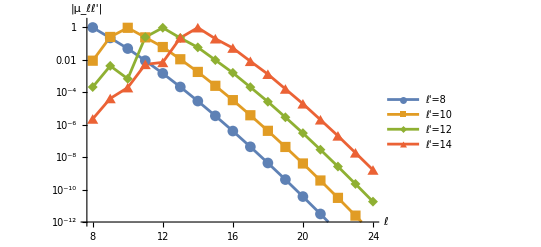

```mathematica
(* c *)
γ[m_,a_]:=Module[
{rISCO,Ω},
rISCO = KerrGeoISCO[a,1];
Ω=1/(rISCO^(3/2)+a);
m a Ω
]
lmax=8;
m=lmax;
a=0.998`20;

mu=muMatrix[m,γ[m,a],24,14,20];
ListLogPlot[Table[Abs[mu[[All,lp-7]]],{lp,{8,10,12,14}}],DataRange->{8,24},Joined->True,PlotMarkers->Automatic,PlotLegends->{"ℓ'=8","ℓ'=10","ℓ'=12","ℓ'=14"},AxesLabel->{"ℓ","|μ_ℓℓ'|"},PlotRange->{10^-12,2}]
```

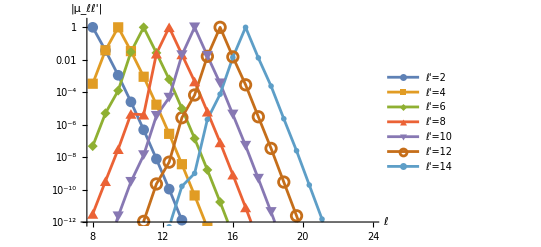

```mathematica
mu2=muMatrix[2,0.2`30,24,14,10];
ListLogPlot[Table[Abs[mu2[[All,lp-1]]],{lp,{2,4,6,8,10,12,14}}],DataRange->{8,24},Joined->True,PlotMarkers->Automatic,PlotLegends->{"ℓ'=2","ℓ'=4","ℓ'=6","ℓ'=8","ℓ'=10","ℓ'=12","ℓ'=14"},AxesLabel->{"ℓ","|μ_ℓℓ'|"},PlotRange->{10^-12,2}]
```

#### Solution

```mathematica
muCol[lp_,m_,γ_,lmaxRow_,n_:10]:=Module[{lmin=Max[Abs[s],Abs[m]],Sf,c,l0},If[γ==0,Return[Table[If[l==lp,1,0],{l,lmin,lmaxRow}]]];Sf=SpinWeightedSpheroidalHarmonicS[s,lp,m,γ,Method->{"SphericalExpansion","NumTerms"->n}];c=Association[Rest[Sf[[1]]["Method"]]]["Coefficients"];l0=lp-Min[lp-lmin,n];Table[If[l0<=l<=l0+Length[c]-1,c[[l-l0+1]],0],{l,lmin,lmaxRow}]];
muMatrix[m_,γ_,lmaxRow_,lmaxCol_,n_:10]:=Transpose[Table[muCol[lp,m,γ,lmaxRow,n],{lp,Max[Abs[s],Abs[m]],lmaxCol}]];
```

```mathematica
Max[Abs[muMatrix[2,g,6,6]-muSpec[[1;;5,1;;5]]]]
```

```mathematica
Max[Abs[muMatrix[2,g,12,6,10]-muMatrix[2,g,12,6,20]]]
```

```mathematica
rI=KerrGeoISCO[0.998`30,1];γmax=8*0.998`30/(rI^(3/2)+0.998`30)
```

3.363456362270127165052611895

```mathematica
μbig=muMatrix[8,γmax,24,14,20];
ListLogPlot[Table[Abs[μbig[[All,lp-7]]],{lp,{8,10,12,14}}],DataRange->{8,24},Joined->True,PlotMarkers->Automatic,PlotLegends->{"ℓ'=8","ℓ'=10","ℓ'=12","ℓ'=14"},AxesLabel->{"ℓ","|μ_ℓℓ'|"},PlotRange->{10^-12,2}]
```

-Graphics-

At γ ≈ 3.4 the first off-diagonal entries are tens of percent. So near ISCO at high spin the spherical ℓ = lmax mode needs spheroidal ℓ' a few beyond lmax (Section 7).

## 5. Use the same S as the Teukolsky amplitude

C^up_ℓ'm is defined relative to a specific S_ℓ'm: the one stored in the mode, which TeukolskyPointParticleMode computes with the Leaver method. If its sign or normalisation differed from the spectral one, the C_ℓm would come out wrong without any error. So check it once.

```mathematica
orb=KerrGeoOrbit[0.9`30,4`30,0,1];
md=TeukolskyPointParticleMode[s,3,2,orb];
SL=md[[1]]["AngularFunction"];
{SL[[1]]["Method"][[1]],SL[[1]]["γ"],0.9`30md["ω"],0.9`30*2/(4`30^(3/2)+0.9`30)}
```

{Leaver,0.20224719101123595505617977528,0.20224719101123595505617977528,0.20224719101123595505617977528}

γ stored in the mode is a·ω with ω = mΩ = m/(r^{3/2} + a), as expected.

### Exercise 5

(a) Compare SL[θ, 0] with Σ_ℓ μ_ℓ3 Y_ℓ2(θ) (use muCol) at θ = 0.3, 1.2, 2.5. (b) Retrograde: compute the ℓ' = 2, m = 2 mode for KerrGeoOrbit[0.9`30, 8`30, 0, -1]. What are the signs of ω and of γ? Compare γ with Honet's γ_m = m χ Ω̂, Ω̂ = 1/(χ + r^{3/2}) with χ = -0.9.

```mathematica
μ=muCol[SL[[1]]["l"],SL[[1]]["m"],SL[[1]]["γ"],16,12];
Table[SL[θ,0]-Sum[μ[[i]]*Y[i+1,SL[[1]]["m"],θ],{i,1,Length[μ]}],{θ,{0.3,1.2,2.5}}]
```

{-1.22125×10^-15,1.11022×10^-16,0.}

```mathematica
orbR=KerrGeoOrbit[0.9`30,8`30,0,-1];
mdR=TeukolskyPointParticleMode[s,2,2,orbR];
SLR=mdR[[1]]["AngularFunction"];
{SLR[[1]]["Method"][[1]],SLR[[1]]["γ"],0.9`30mdR["ω"],-0.9`30*2/(8`30^(3/2)-0.9`30)}
2*(-0.9)*1/(8^(3/2)-0.9)
```

{Leaver,-0.082844638189998116953556672,-0.082844638189998116953556672,-0.082844638189998116953556672191}

-0.0828446

#### Solution

```mathematica
col=muCol[3,2,SL[[1]]["γ"],16,12];
Table[SL[θ,0]-col.Table[Y[l,2,θ],{l,2,16}],{θ,{0.3`30,1.2`30,2.5`30}}]
```

{0.,0.,-6.×10^-26}

```mathematica
mdR=TeukolskyPointParticleMode[s,2,2,KerrGeoOrbit[0.9`30,8`30,0,-1]];
{mdR["ω"],mdR[[1]]["AngularFunction"][[1]]["γ"],2(-0.9`30)/(-0.9`30+8`30^(3/2))}
```

{-0.092049597988886796615062969,-0.082844638189998116953556672,-0.082844638189998116953556672191}

For the retrograde orbit the package has Ω_φ < 0, so ω = mΩ_φ < 0 and γ = aω < 0. This is the same number as Honet's γ_m = mχΩ̂. So μ(m, γ) built from the mode's own γ is the right matrix in both conventions. Beware that the two frames differ by a flip of the z axis (φ → -φ). The package's mode m in the retrograde case is not Honet's mode m, though |C_ℓm| agree by the symmetry of Section 2. Fix this when you define the phases δφ_ℓm.

## 6. What the change of basis does at one orbit

Physics: notes/spheroidal_to_spherical.pdf, Section 3 (eqs. 8-9, Table 1). From here on all data handling is given. The spheroidal amplitudes Cup for six orbits are precomputed in data/sphdAmps_examples.m (m = 2, 4, 6, 8; columns l' = max(2,m) ... 14; at least 12 digits each), so every cell runs in seconds. Spend the time on the questions, not on the code.

### Toolbox (given: just run it)

Needs muMatrix from the Exercise 4 solution. amps[key, m] returns <|"omega", "gamma", "lp", "Cup", "prec"|> for one orbit and one m. toSpherical[m, γ, Cup, lRowMax] returns the spherical C_l for l = max(2,m) ... lRowMax, using all the columns you pass. cTrunc and errTrunc are for Exercise 7. chiOf is Honet's signed χ, vOf = |Ω|^(1/3). Orbit keys: a = spin, r = r0, isco = 1.05 r_ISCO prograde, retro = retrograde.

```mathematica
dataDir = If[TrueQ[$Notebooks], FileNameJoin[{NotebookDirectory[], "data"}], FileNameJoin[{Directory[], "data"}]];
sphdData = Get[FileNameJoin[{dataDir, "sphdAmps_examples.m"}]];
orbits = Keys[sphdData]
amps[key_, m_] := sphdData[key]["modes"][m];
chiOf[key_] := sphdData[key]["a"] sphdData[key]["x"];
vOf[key_] := Abs[amps[key, 2]["omega"]/2]^(1/3);
muM[m_, g_, lr_, lc_] := muM[m, g, lr, lc] = muMatrix[m, g, lr, lc, 20];
toSpherical[m_, g_, Cup_List, lRowMax_] := muM[m, g, lRowMax, Max[2, Abs[m]] + Length[Cup] - 1] . Cup;
cTrunc[key_, m_, L_, Lp_] := With[{d = amps[key, m]}, toSpherical[m, d["gamma"], Take[d["Cup"], Lp - Max[2, m] + 1], L]];
errTrunc[key_, m_, L_, Lp_] := Abs[cTrunc[key, m, L, Lp]/cTrunc[key, m, L, 14] - 1];
```

### Exercise 6

Question: which spherical modes does the change of basis actually change, and by how much?

(a) Orbit "a0.9_r4", m = 2. Compute the spherical C_l (rows up to 14, all stored columns) and plot |Cup_l'| and |C_l| against l on a log scale. Before looking, predict which l change most from the parity rule C_lm ~ v^l for l+m even, v^(l+1) for l+m odd (notes eq. 8). Then tabulate |C_l - Cup_l|/|C_l| for l = 2 ... 8.

(b) One term at a time. To first order, C_32 ≈ Cup_32 + μ_32 Cup_22 and C_22 ≈ μ_22 Cup_22 + μ_23 Cup_32 (Honet A26). Read μ_32, μ_23 and μ_22 - 1 from muM[2, γ, 14, 14] and find which fraction of the shifts C_32 - Cup_32 and C_22 - Cup_22 each term explains. Is μ_32/γ of order 1/l (notes eq. 6)?

(c) Scaling. For all six orbits, plot the relative change of (3,2) against |χ| v and that of (2,2) against |χ| v^5. Do the points line up through the origin? Which orbit departs, and why?

(d) Flux. At "a0.9_isco", m = 2, compare Σ|C_l|^2 with Σ|Cup_l'|^2, with rows up to 14 and up to 8. Does the flux grid have to be recomputed in the spherical basis?

#### Solution

```mathematica
d6 = amps["a0.9_r4", 2];
C6 = toSpherical[2, d6["gamma"], d6["Cup"], 14];
ListLogPlot[{Transpose[{d6["lp"], Abs[d6["Cup"]]}], Transpose[{Range[2, 14], Abs[C6]}]}, Joined -> True, PlotMarkers -> Automatic, PlotLegends -> {"spheroidal |Cup_l'|", "spherical |C_l|"}, AxesLabel -> {"l", ""}]
TableForm[Table[{l, N[Abs[(C6[[l - 1]] - d6["Cup"][[l - 1]])/C6[[l - 1]]], 3]}, {l, 2, 8}], TableHeadings -> {None, {"l", "|C - Cup|/|C|"}}]
```

(2,2) moves by 2e-3, every l ≥ 3 by 40-60%. (3,2) sits next to the dominant (2,2), which is v^-2 louder; each even-parity l ≥ 4 sits next to the louder odd-parity mode just below it. An O(γ) share of a louder neighbour is a large relative change (notes eq. 9).

```mathematica
g6 = d6["gamma"]; mu6 = muM[2, g6, 14, 14];
N[{mu6[[2, 1]], mu6[[1, 2]], mu6[[1, 1]] - 1, mu6[[2, 1]]/g6}, 4]
(* fraction of each shift explained by one term: (3,2) by mu_32 Cup_22; (2,2) by mu_23 Cup_32 and by (mu_22 - 1) Cup_22 *)
N[{mu6[[2, 1]] d6["Cup"][[1]]/(C6[[2]] - d6["Cup"][[2]]), mu6[[1, 2]] d6["Cup"][[2]]/(C6[[1]] - d6["Cup"][[1]]), (mu6[[1, 1]] - 1) d6["Cup"][[1]]/(C6[[1]] - d6["Cup"][[1]])}, 3]
```

μ_32 Cup_22 accounts for the whole shift of (3,2) (ratio ≈ 1). For (2,2) the O(γ) term μ_23 Cup_32 explains only about 60%: it is suppressed by Cup_32/Cup_22 ~ v^2, so the O(γ^2) normalisation term (μ_22 - 1) Cup_22 is comparable (about 40%). This is the structure of Honet (A26). μ_32/γ ≈ 0.19, of order 1/l.

```mathematica
rel[key_, l_] := With[{d = amps[key, 2]}, With[{C = toSpherical[2, d["gamma"], d["Cup"], 14]}, Abs[(C[[l - 1]] - d["Cup"][[l - 1]])/C[[l - 1]]]]];
tab6 = Table[N[{k, Abs[chiOf[k]] vOf[k], rel[k, 3], rel[k, 3]/(Abs[chiOf[k]] vOf[k]), Abs[chiOf[k]] vOf[k]^5, rel[k, 2], rel[k, 2]/(Abs[chiOf[k]] vOf[k]^5)}, 3], {k, orbits}];
TableForm[tab6, TableHeadings -> {None, {"orbit", "|chi| v", "rel (3,2)", "ratio", "|chi| v^5", "rel (2,2)", "ratio"}}]
GraphicsRow[{ListPlot[tab6[[All, {2, 3}]], AxesLabel -> {"|chi| v", "(3,2)"}, PlotRange -> {{0, All}, {0, All}}, PlotMarkers -> Automatic], ListPlot[tab6[[All, {5, 6}]], AxesLabel -> {"|chi| v^5", "(2,2)"}, PlotRange -> {{0, All}, {0, All}}, PlotMarkers -> Automatic]}, ImageSize -> 700]
```

(3,2): ratio 1.2-1.5, roughly a line through the origin: the shift is a 0.5PN-relative spin effect, ∝ χ v. The ratio grows with χ v (higher orders in γ), and at χ = 0.998 the relative change exceeds 1: the spherical (3,2) is almost all leakage from (2,2). (2,2): ratio 0.04-0.14, so ∝ χ v^5 up to the O(γ^2) term of (b).

```mathematica
d6i = amps["a0.9_isco", 2];
N[{Total[Abs[toSpherical[2, d6i["gamma"], d6i["Cup"], 14]]^2], Total[Abs[toSpherical[2, d6i["gamma"], d6i["Cup"], 8]]^2]}/Total[Abs[d6i["Cup"]]^2] - 1, 3]
```

Rows up to 14: equal to working precision. Rows up to 8: the missing power is ~1e-18. The flux is basis independent (notes Section 3), so the flux grid stays as it is; only amplitudes and phases need the change of basis. For m < 0 nothing new: C_{l,-m} = (-1)^l C*_{lm} in the spherical basis, so compute m > 0 only.

## 7. Truncation in l'

Physics: notes Section 4. Three different cuts appear: the package's NumTerms (harmless), the rows l ≤ L you keep (a modelling choice that does not change any kept C_lm), and the columns l' ≤ L' you computed. Only the last one is an error on the amplitudes you keep: C_lm misses Σ_{l' > L'} μ_{l l'} Cup_l'm (notes eq. 10).

### Exercise 7

Question: where does cutting the spheroidal sum hurt, and how many extra spheroidal modes does the grid rerun need? Keep the rows fixed at l ≤ L = 8 throughout, so only the columns L' = L + Δ change. The reference is all stored columns (l' ≤ 14); errTrunc[key, m, L, L'] gives the relative error of every row.

(a) Orbit "a0.9_isco", m = 2. Plot the relative error against l for Δ = 0, 1, 2, 4. Where is the error, and how much does each extra spheroidal mode buy?

(b) Error model. The first omitted spheroidal mode contributes μ_{l,L'+1} Cup_{L'+1}. Compute it (one column of muM times one amplitude) and compare with the true error from (a). What does this give you for free on every grid node?

(c) Worst case. For every orbit and m = 2, 4, 6, 8, compute the error at l = L with Δ = 0 and plot it against |γ_m|. Which (orbit, m) is worst? Why is the trend clean for m = 8 but not for m = 2 (notes Section 4, item 3)?

(d) Decide. Which Δ keeps the worst case below 1e-4 (interpolation error of the current 18x27 grid, benchmarks.md) and below 1e-10 (Honet's refined grid)? This Δ goes into Section 8.

#### Solution

```mathematica
L = 8;
ListLogPlot[Table[Transpose[{Range[2, L], errTrunc["a0.9_isco", 2, L, L + dl]}], {dl, {0, 1, 2, 4}}], Joined -> True, PlotMarkers -> Automatic, PlotLegends -> {"Δ = 0", "Δ = 1", "Δ = 2", "Δ = 4"}, AxesLabel -> {"l", "rel. error"}]
```

The error sits in the top row l = L: one row lower it is 4 orders smaller. Each extra spheroidal mode buys 2-4 orders.

```mathematica
estTrunc[key_, m_, L_, Lp_] := With[{d = amps[key, m], lmin = Max[2, m]}, Abs[muM[m, d["gamma"], L, Lp + 1][[All, -1]] d["Cup"][[Lp + 2 - lmin]]/cTrunc[key, m, L, 14]]];
TableForm[Transpose[{Range[2, L], N[errTrunc["a0.9_isco", 2, L, L], 2], N[estTrunc["a0.9_isco", 2, L, L], 2]}], TableHeadings -> {None, {"l", "true error", "one-term estimate"}}]
```

The one-term estimate matches the true error in every row. So on the grid, compute one spheroidal mode more than you use: its contribution is a node-by-node error estimate at no extra cost.

```mathematica
worst = Flatten[Table[{Abs[amps[k, mm]["gamma"]], Last[errTrunc[k, mm, L, L]], k, mm}, {k, orbits}, {mm, {2, 4, 6, 8}}], 1];
ListLogPlot[Table[Select[worst, #[[4]] == mm &][[All, {1, 2}]], {mm, {2, 4, 6, 8}}], PlotMarkers -> Automatic, PlotLegends -> {"m = 2", "m = 4", "m = 6", "m = 8"}, AxesLabel -> {"|γ_m|", "error at l = L, Δ = 0"}]
N[Take[SortBy[worst, -#[[2]] &], 3], 3]
```

Worst: l = m = 8 at χ = 0.998 near the ISCO, about 1e-2. At m = L the only kept mode, l = m, is the loudest of its m and sits at the cut, so the error grows cleanly with γ. For m < L the denominator C_Lm is itself fed by louder modes below, so a larger γ can lower the relative error (m = 2 at χ = 0.998 is smaller than at χ = 0.9).

```mathematica
TableForm[Table[{dl, N[Max[Table[Last[errTrunc[k, mm, L, L + dl]], {k, orbits}, {mm, {2, 4, 6, 8}}]], 2]}, {dl, 0, 4}], TableHeadings -> {None, {"Δ", "worst error at l = L"}}]
```

Δ = 1 already gives 4e-5 < 1e-4; take Δ = 2 (4e-7) for margin on the current grid. Δ = 3 gives 1.6e-9, so the refined grid needs Δ = 4 (7e-12).

#### Your attempt at the old Exercise 6 (kept for reference)

```mathematica
a=0.9`30;
r0=4`30;
orb=KerrGeoOrbit[a,r0,0,1];

m=2;
lmin=Max[2,Abs[m]];
lmax=6;

modes = Table[TeukolskyPointParticleMode[s,l,m,orb],{l,lmin,lmax}];
γ=modes[[1]]["AngularFunction"][[1]]["γ"];
μ=muMatrix[m,γ,lmax,lmax,15];

Cspheroidal[lp_,m_]:=modes[[lp-lmin+1]]["Amplitudes"]["ℐ"];
CspheroidalVec=Table[Cspheroidal[lp,m],{lp,lmin,lmax}];
CsphericalVec=μ.CspheroidalVec;
Cspherical[l_]:=CsphericalVec[[l-lmin+1]];

hlmVec=(2 CsphericalVec)/(γ/a)^2;
```

```mathematica
With[
{θ=1.1},
oid=CspheroidalVec.(#[[1]]["AngularFunction"][θt,0]&/@modes);
eri=CsphericalVec.Table[Y[l,2,θ],{l,lmin,lmax}];
]
oid-eri
```

-1.75072×10^-9+2.5684×10^-9 ⅈ

## 8. Toward the Honet grid (no solution: this is your code)

What the production code needs, per Chebyshev node (i, j) of FluxesGrid.nb and per m = 1 … lmax:

New data: the flux grid stores only fluxes. Rerun the grid (same nodeOrbit, same precision ladder) and keep md["Amplitudes"]["ℐ"] (and "ℋ" if you want horizon amplitudes) for l' up to lmax + Δ, with Δ from Exercise 7d (2 for the current grid, 4 for 1e-10), plus one more l' as an error estimate (Exercise 7b).

γ_m from the mode (= mχΩ̂_ij with Ω̂_ij = (χ_j + (2r*/(r_C,i + 1))^{3/2})^{-1}, Honet (A27)), and the μ matrix from muMatrix. Check NumTerms convergence at the worst node.

C_ℓm = μ . C_ℓ'm (A27), keeping ℓ ≤ lmax.

Rescale before interpolating: c_ℓm = r_p^{ℓ/2} C_ℓm/Ω̂.b2 for ℓ + m even, r_p^{(1+ℓ)/2} C_ℓm/Ω̂.b2 for ℓ + m odd, with r_p = 2r*/(r_C + 1) (A28, A29). Then use the Chebyshev machinery of FluxInterpolation.wl.

Reconstruct C_ℓm(Ω̂, χ) with (A30, A31), and the real amplitudes ĥ_ℓm and phases δφ_ℓm with (52)-(54).

Decide the retrograde convention (Section 5) before you define phases.

Further reading if you want the derivations: S. A. Hughes, PRD 61, 084004 (2000), appendix on the spectral method for spheroidal harmonics; G. B. Cook and M. Zalutskiy, PRD 90, 124021 (2014), for the Clebsch–Gordan form of the matrix and the sign conventions.